# Laplace Transforms

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

## iSIM problem

```mathematica
With[{context="isim`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
true=-m g l Sin[θ[t]]-d θ'[t]==i θ''[t];
linearized=true/.Sin[θ[t]]->θ[t]
```

-g l m θ[t]-d θ'[t]==i θ''[t]

```mathematica
params=<|
m->QuantityMagnitude[UnitConvert[Quantity[0.211, "Pounds"], "Kilograms"]],g->QuantityMagnitude@UnitConvert@Entity["Planet","Earth"]["Gravity"],l->QuantityMagnitude@UnitConvert[Quantity[8.125, "Inches"], "Meters"],i->QuantityMagnitude@UnitConvert[Quantity[19.2, ("Inches")^2 "PoundsForce"], "Meters"^2*"Newtons"]|>
```

<|m→0.095708,g→9.8,l→0.206375,i→0.0551004|>

```mathematica
components={θdot,-m g l θ-d θdot};
Manipulate[StreamPlot[components/.params/.d->dval,{θ,-Pi,Pi},{θdot,-Pi,Pi},FrameLabel->{"θ","ω"}],{dval,0,2},SaveDefinitions->True]
CloudDeploy[%,Permissions->"Public"]
```

CloudObject[]

```mathematica
Solve[r^2+d r+mgl==0,r]
```

{{r→1/2 (-d-√(d^2-4 mgl))},{r→1/2 (-d+√(d^2-4 mgl))}}

```mathematica
sol=DSolveValue[linearized,θ[t],t]
```

ⅇ^(1/2 (-(isim`d)/(isim`i)-(√((isim`d)^2-4 isim`g isim`i isim`l isim`m))/(isim`i)) t) C[1]+ⅇ^(1/2 (-(isim`d)/(isim`i)+(√((isim`d)^2-4 isim`g isim`i isim`l isim`m))/(isim`i)) t) C[2]

```mathematica
Manipulate[Plot[sol/.params/.d->dval/.{C[1]->1,C[2]->1},{t,0,10},PlotRange->Full],{dval,0,.3},SaveDefinitions->True]
CloudDeploy[%,Permissions->"Public"]
```

CloudObject[]

```mathematica
With[{context="isim`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Laplace

```mathematica
With[{context="l`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
bigY=(s+1)/(s^2+5s+4)
Apart[bigY]
InverseLaplaceTransform[bigY,s,t]
```

(1+s)/(4+5 s+s^2)

1/(4+s)

ⅇ^(-4 t)

```mathematica
bigY=1/(s^2+2s+2)
split=Apart[bigY]
InverseLaplaceTransform[#,s,t]&/@split
FullSimplify@InverseLaplaceTransform[bigY,s,t]
```

1/(2+2 s+s^2)

1/(2+2 s+s^2)

(2 DiracDelta[t]+2 DiracDelta'[t]+DiracDelta''[t])^(-DiracDelta[t])

ⅇ^-t Sin[t]

```mathematica
LaplaceTransform[f'''[t],t,s]//TraditionalForm
```

s^3 (ℒ_t[f(t)](s))-f''(0)-s f'(0)-f(0) s^2

```mathematica
With[{context="l`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Scratch Work

```mathematica
exportNotebookPDF[]
```

/home/eric/Documents/School/QEA2/Module 3/Laplace Transforms/Mathematica work.pdf

1/(s^2+2s+2)

```mathematica
EmbedCode[CloudDeploy[APIFunction[{"City"->"String"},WeatherData[#city,"Temperature"]&],Permissions->"Public"],"Python"]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from Python:
Code
 | Copy to Clipboard
from urllib import urlencode
from urllib2 import urlopen

class WolframCloud:

    def wolfram_cloud_call(self, **args):
        arguments = dict([(key, arg) for key, arg in args.iteritems()])
        result = urlopen("http://www.wolframcloud.com/objects/b59d9861-219a-4cc6-868a-ea3cde7c09a5", urlencode(arguments))
        return result.read()

    def call(self, City):
        textresult =  self.wolfram_cloud_call(City=City)
        return textresult

```mathematica
WeatherData["Boston","Temperature"]
```

14.4

```mathematica
Rotate[{1,0},Pi/3]
```

{1,0}

```mathematica
FileNames["/dev/ttyACM*"]
```

{/dev/ttyACM0}

```mathematica
findArduino[]
```

/dev/ttyACM0

OptionValue::nodef: Unknown option ArduinoInstallLocation for ArduinoLink`Private`ArduinoOpenDriver.

DeviceObject[…]

```mathematica
arduino
```

DeviceObject[…]

```mathematica
DeviceClose[arduino]
```

```mathematica
DeviceOpen["Arduino","/dev/ttyACM0"]
```

SerialLink`SerialPortOpen::nopen: Could not open the port /dev/ttyACM0.

$Failed

```mathematica
LaplaceTransform[θ'[t],t,s]//TraditionalForm
```

s (ℒ_t[θ(t)](s))-θ(0)

```mathematica
$UserBaseDirectory
```

/home/eric/.Mathematica

```mathematica
DeviceReadTimeSeries
```

```mathematica
ts=DeviceReadTimeSeries["Arduino",{3,.01},"A0"]
ts=TimeSeriesResample[ts]
```

DeviceReadTimeSeries::tslow: The result may have taken longer to obtain and/or may have a smaller number of data points because 178 measurement(s) took longer than the requested interval 0.01, about 0.0115061 seconds (on average).

TimeSeries[…]

TimeSeries[…]

TimeSeries[…]

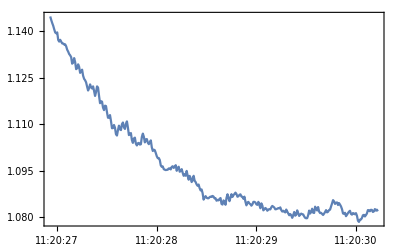

```mathematica
smoothed=MovingAverage[ts,Quantity[100, "Milliseconds"]]
DateListPlot[smoothed]
```

```mathematica
arduino//InputForm
```

DeviceObject[{"Arduino", 2}]

InterpolatingFunction[{{0., 5.}}, <>][t]

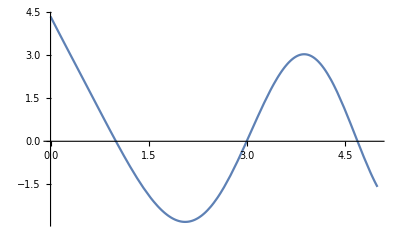

```mathematica
NDSolveValue[{f''[t]==-t f[t]+1,f[3]==f[1]==0},f[t],{t,0,5}]

Plot[%,{t,0.,5.}]
```

```mathematica
DeviceRead["Arduino","A0"]
```

1.1437 V